```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ken_l/Documents/active-ads/images

```mathematica
d=-0.3;Graph[{"r","a","b","e","f","c","d","g","h"},DirectedEdge@@#&/@{{"r","a"},{"a","b"},{"b","e"},{"b","c"},{"e","f"},{"c","d"},{"d","g"},{"g","h"}},VertexCoordinates->{{0,0},{-1,d},{-0.5,2d},{-0.75,3d},{-0.55,4d},{-0.25,3d},{0,4d},{-0.15,5d},{0.0,6d}},VertexLabels->Placed["Name",Center],VertexSize->0.25,VertexStyle->White]//Export["fig-ort-to-bt_sol.png",#,"PNG"]&
```

fig-ort-to-bt_sol.png

```mathematica
d=-0.25;w=0.5;
BTpositions={{0,0},{-w,d},{w,d},{-1.25w,2d},{-0.75w,2d},{0.75w,2d},{1.25w,2d},{-1.4w,3d},{-1.1w,3d},{-0.9w,3d},{-0.6w,3d}}
```

(0 | 0
-0.5 | -0.25
0.5 | -0.25
-0.625 | -0.5
-0.375 | -0.5
0.375 | -0.5
0.625 | -0.5
-0.7 | -0.75
-0.55 | -0.75
-0.45 | -0.75
-0.3 | -0.75)

```mathematica
BTedges=UndirectedEdge@@#&/@{{1,2},{1,3},{2,4},{2,5},{3,6},{3,7},{4,8},{4,9},{5,10},{5,11}}
```

{1<->2,1<->3,2<->4,2<->5,3<->6,3<->7,4<->8,4<->9,5<->10,5<->11}

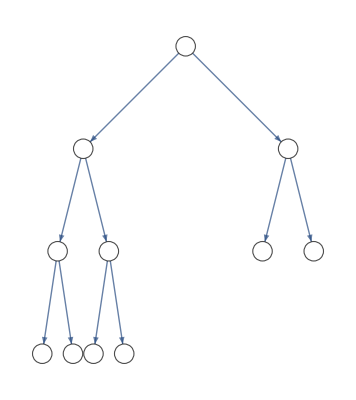

```mathematica
Graph[Range[11],BTedges,VertexCoordinates->BTpositions,VertexLabels->Placed["Name",Center],VertexSize->0.95,VertexStyle->White]
```

```mathematica
vsequence={{1,2,4,8},{1,2,4,5},{1,2,4,9},{1,2,5,10},{1,2,5,11}}
```

(1 | 2 | 4 | 8
1 | 2 | 4 | 5
1 | 2 | 4 | 9
1 | 2 | 5 | 10
1 | 2 | 5 | 11)

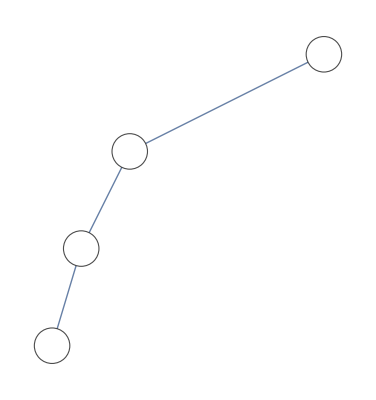
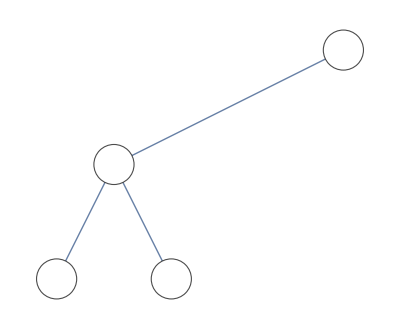
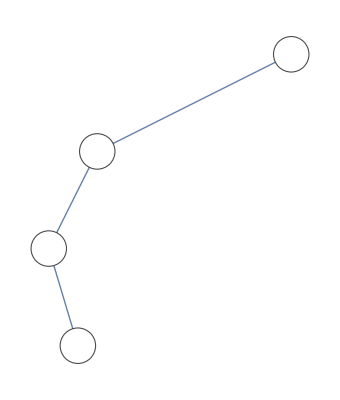
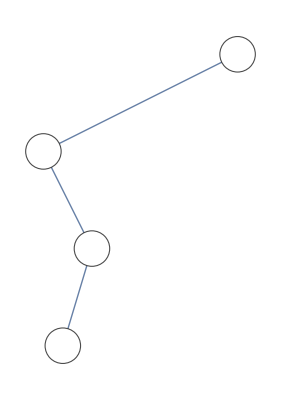
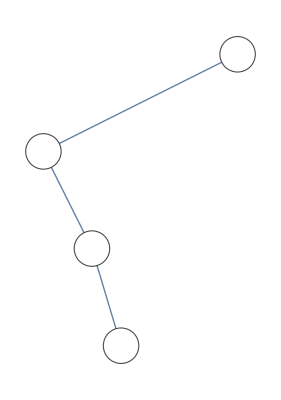

```mathematica
btrees=Map[(v=#;Graph[v,Select[BTedges,SubsetQ[v,List@@#]&],VertexCoordinates->BTpositions[[v]],VertexSize->0.35,VertexStyle->White])&,vsequence]
```

```mathematica
d=-0.5;w=0.5;
ORTpositions={{0,0},{-w,d},{w,d},{-1.25w,2d},{-0.75w,2d},{0.75w,2d},{1.25w,2d},{0,d},{0,2d},{0,3d},{-w,2d},{w,2d}}
```

(0 | 0
-0.5 | -0.5
0.5 | -0.5
-0.625 | -1.
-0.375 | -1.
0.375 | -1.
0.625 | -1.
0 | -0.5
0 | -1.
0 | -1.5
-0.5 | -1.
0.5 | -1.)

```mathematica
ORTedges=UndirectedEdge@@#&/@{{1,2},{1,8},{1,3},{2,4},{2,5},{8,9},{9,10},{3,6},{3,7},{8,5},{8,6},{2,11},{3,12}}
```

{1<->2,1<->8,1<->3,2<->4,2<->5,8<->9,9<->10,3<->6,3<->7,8<->5,8<->6,2<->11,3<->12}

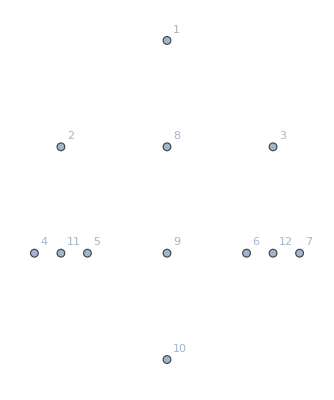

```mathematica
Graph[Range[Length[ORTpositions]],{},VertexCoordinates->ORTpositions,VertexLabels->"Name"]
```

```mathematica
ORTsequence={{1,8,9,10},{1,2,11,3},{1,8,5,6},{1,2,3,12},{1,2,8,3}}
```

(1 | 8 | 9 | 10
1 | 2 | 11 | 3
1 | 8 | 5 | 6
1 | 2 | 3 | 12
1 | 2 | 8 | 3)

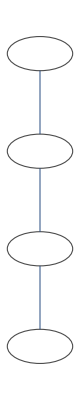
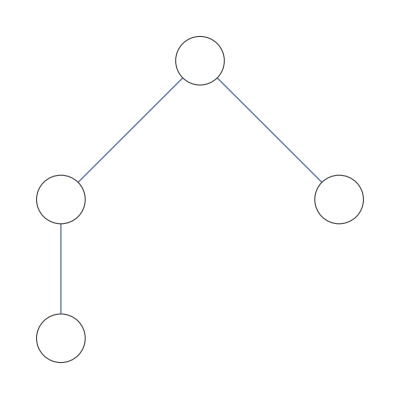
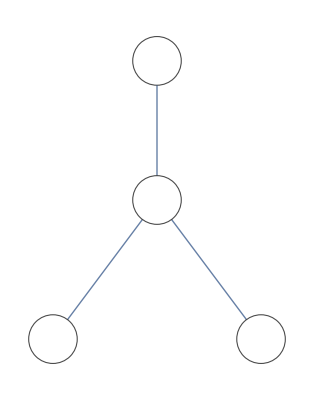
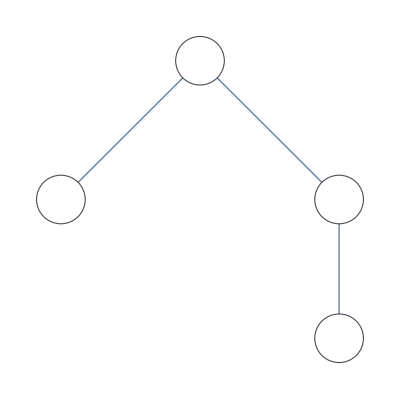
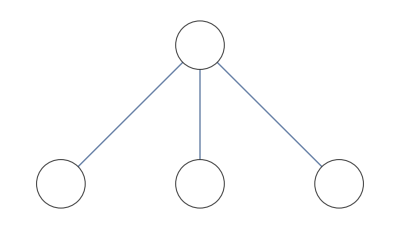

```mathematica
rtrees=Map[(v=#;Graph[v,Select[ORTedges,SubsetQ[v,List@@#]&],VertexCoordinates->ORTpositions[[v]],VertexSize->0.35,VertexStyle->White])&,ORTsequence]
```

```mathematica
GraphicsGrid[{btrees,rtrees}//Transpose//Prepend[#,{Text[Style["Left Binary\nTrees",Small]]//Graphics,Text[Style["Corresponding\nRooted Trees",Small]]//Graphics}]&//Transpose]//Export["fig-tree_correspondence.png",#,"PNG"]&
```

fig-tree_correspondence.png

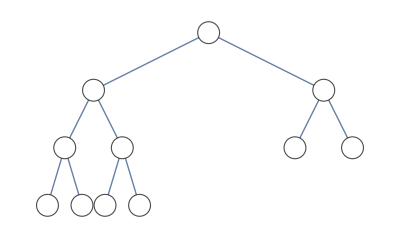
Canvas[-Graphics-]

```mathematica
Graph[Range[11],BTedges,VertexCoordinates->BTpositions,VertexLabels->Placed["Name",Center],VertexSize->0.95,VertexStyle->White]//Canvas
```